```mathematica
GenMatrix2[g_,vertices_]:=Block[
{result=Table[-1,{i,1,5},{j,1,5}],i,j, v1, v2, graph2,vert, div},
For[i=1,i≤4,i++,
v1=vertices[[i]];
For[j=1,j≤i,j++,
v2=vertices[[j]];
If[i==j,
vert={v1<->vertices[[Mod[i+1,4]+1]],v1<->vertices[[Mod[i+2,4]+1]]};
graph2=EdgeAdd[g,vert];
result[[i,j]]=ChromaticPolynomial[graph2,4]/24
,
graph2=EdgeAdd[g,v1<->v2];
result[[i,j]]=ChromaticPolynomial[graph2,4]/24;
result[[j,i]]=result[[i,j]]
]
];
];
div=result[[1,2]];
For[i=1,i≤4,i++,
result[[i,5]]=Sum[result[[i,k]],{k,1,4}]-result[[i,i]]-2*result[[i,Mod[i,4]+1]];
result[[5,i]]=Sum[result[[k,i]],{k,1,4}]-result[[i,i]]-2*result[[Mod[i,4]+1,i]];
];

result[[5,5]]=Sum[result[[5,k]],{k,1,5}]/div;
For[i=1,i≤4,i++,
result[[i,i]]=Style[result[[i,i]],Bold, Red];
result[[i,Mod[i,4]+1]]=Style[result[[i,Mod[i,4]+1]],Italic, Blue];
result[[i,Mod[i+2,4]+1]]=Style[result[[i,Mod[i+2,4]+1]],Italic,Blue];
];
result]
```

```mathematica
Take[deps2,3]
```

{{1,2,{2,1<->4,2<->3}},{2,3,{2,2<->4,3<->5}},{2,4,{2,2<->5,1<->4}}}

```mathematica
{{1,2,"{2,1<->4,2<->3}"},{2,3,"{2,2<->4,3<->5}"},{2,4,"{2,2<->5,1<->4}"}}
```

```mathematica
deps2=ReadList["D:\\Grofs\\dependencies2.txt",Expression];Length[deps2]
```

1365053

```mathematica
Sort[
Tally[
Monitor[

Table[
With[{record=deps2[[k]]},
With[
{rule=Read[StringToStream[record[[3]]]]},
With[
{g=MyEdgeDelete[ReadGrof[record[[1]]],{rule[[2]]}],vertices={rule[[2,1]],rule[[3,1]],rule[[2,2]],rule[[3,2]]}},
With[
{div=ChromaticPolynomial[g,4]},
Sort[{ChromaticPolynomial[EdgeAdd[g,rule[[2]]],4]/div,ChromaticPolynomial[EdgeAdd[g,rule[[3]]],4]/div}]
]
]
]
],
{k,Length[deps2]-1000,Length[deps2]}
],
k]
]
]
```

{{{1/513,341/513},2},{{1/257,172/257},5},{{1/129,85/129},12},{{1/65,44/65},6},{{1/33,7/11},4},{{1/33,89/132},4},{{1/17,43/68},6},{{1/17,12/17},4},{{1/9,5/9},7},{{1/9,25/36},5},{{1/5,11/20},2},{{1/5,4/5},168},{{1/3,1/3},263},{{1/3,13/24},3},{{1/3,3/4},3},{{1/3,8/9},4},{{3/8,1/2},11},{{5/12,2/3},3},{{1/2,1},433},{{86/171,341/342},1},{{2/3,5/6},53},{{7/10,4/5},2}}

```mathematica
Monitor[

Table[
With[{record=deps2[[k]]},
With[
{rule=Read[StringToStream[record[[3]]]]},
With[
{g=MyEdgeDelete[ReadGrof[record[[1]]],{rule[[2]]}],vertices={rule[[2,1]],rule[[3,1]],rule[[2,2]],rule[[3,2]]}},
MatrixForm[GenMatrix2[g,vertices]]
]
]
],
{k,1,2}
],
k]
```

{(1 | 2 | 1 | 2 | 1
2 | 2 | 2 | 2 | 2
1 | 2 | 1 | 2 | 1
2 | 2 | 2 | 2 | 2
1 | 2 | 1 | 2 | 5/2),(1 | 2 | 1 | 2 | 1
2 | 2 | 2 | 2 | 2
1 | 2 | 1 | 2 | 1
2 | 2 | 2 | 2 | 2
1 | 2 | 1 | 2 | 5/2)}

```mathematica
$HistoryLength=1
```

1

```mathematica
draw=Sort[
Tally[
Monitor[

Table[
With[{record=deps2[[k]]},
With[
{rule=Read[StringToStream[record[[3]]]]},
With[
{g=MyEdgeDelete[ReadGrof[record[[1]]],{rule[[2]]}],vertices={rule[[2,1]],rule[[3,1]],rule[[2,2]],rule[[3,2]]}},
With[
{div=ChromaticPolynomial[g,4],vert=ChromaticPolynomial[EdgeAdd[g,rule[[2]]],4], hor=ChromaticPolynomial[EdgeAdd[g,rule[[3]]],4]},
{(div==hor)||(div==vert),vert/div+hor/div,Sort[{vert/div,hor/div},#1>#2&]}
]
]
]
],
{k,1,50000}
],
k]
]
]
```

{{{False,2/3,{1/3,1/3}},8654},{{False,2/3,{25/69,7/23}},3},{{False,2/3,{17/45,13/45}},2},{{False,2/3,{5/12,1/4}},3},{{False,2/3,{3/7,5/21}},263},{{False,2/3,{25/57,13/57}},2},{{False,2/3,{7/15,1/5}},20},{{False,2/3,{1/2,1/6}},46},{{False,2/3,{29/57,3/19}},8},{{False,2/3,{5/9,1/9}},1513},{{False,2/3,{41/69,5/69}},5},{{False,2/3,{7/11,1/33}},58},{{False,2/3,{85/129,1/129}},2},{{False,9/13,{44/65,1/65}},7},{{False,33/47,{22/47,11/47}},2},{{False,5/7,{2/5,11/35}},11},{{False,5/7,{22/35,3/35}},12},{{False,23/32,{3/8,11/32}},41},{{False,21/29,{13/29,8/29}},3},{{False,21/29,{16/29,5/29}},1},{{False,19/26,{1/2,3/13}},17},{{False,36/49,{29/49,1/7}},1},{{False,17/23,{14/23,3/23}},89},{{False,32/43,{29/43,3/43}},7},{{False,3/4,{2/5,7/20}},3},{{False,3/4,{11/20,1/5}},52},{{False,28/37,{15/37,13/37}},5},{{False,28/37,{17/37,11/37}},1},{{False,13/17,{7/17,6/17}},9},{{False,13/17,{8/17,5/17}},21},{{False,13/17,{12/17,1/17}},340},{{False,24/31,{13/31,11/31}},5},{{False,24/31,{17/31,7/31}},3},{{False,11/14,{3/7,5/14}},79},{{False,11/14,{9/14,1/7}},7},{{False,51/64,{7/16,23/64}},2},{{False,4/5,{11/25,9/25}},23},{{False,4/5,{13/25,7/25}},18},{{False,29/36,{25/36,1/9}},4},{{False,9/11,{5/11,4/11}},6},{{False,9/11,{6/11,3/11}},681},{{False,9/11,{8/11,1/11}},2},{{False,43/52,{23/52,5/13}},3},{{False,16/19,{9/19,7/19}},129},{{False,16/19,{13/19,3/19}},105},{{False,23/27,{16/27,7/27}},2},{{False,23/27,{20/27,1/9}},2},{{False,6/7,{3/7,3/7}},3},{{False,6/7,{3/5,9/35}},1},{{False,37/43,{30/43,7/43}},1},{{False,7/8,{7/16,7/16}},3},{{False,7/8,{1/2,3/8}},1236},{{False,7/8,{5/8,1/4}},100},{{False,33/37,{24/37,9/37}},1},{{False,33/37,{28/37,5/37}},40},{{False,26/29,{15/29,11/29}},7},{{False,26/29,{17/29,9/29}},3},{{False,19/21,{10/21,3/7}},30},{{False,19/21,{11/21,8/21}},1},{{False,19/21,{2/3,5/21}},8},{{False,12/13,{7/13,5/13}},89},{{False,12/13,{8/13,4/13}},5},{{False,12/13,{9/13,3/13}},605},{{False,29/31,{22/31,7/31}},21},{{False,17/18,{1/2,4/9}},2},{{False,17/18,{5/9,7/18}},1},{{False,17/18,{11/18,1/3}},24},{{False,22/23,{13/23,9/23}},11},{{False,22/23,{17/23,5/23}},11},{{False,27/28,{15/28,3/7}},4},{{False,27/28,{17/28,5/14}},5},{{False,27/28,{5/7,1/4}},34},{{False,32/33,{23/33,3/11}},3},{{False,52/53,{41/53,11/53}},9},{{False,1,{1/2,1/2}},49},{{False,1,{13/25,12/25}},1},{{False,1,{8/15,7/15}},7},{{False,1,{3/5,2/5}},326},{{False,1,{16/25,9/25}},3},{{False,1,{2/3,1/3}},9},{{False,1,{11/15,4/15}},4},{{False,1,{4/5,1/5}},6084},{{False,53/52,{41/52,3/13}},5},{{False,48/47,{33/47,15/47}},1},{{False,33/32,{23/32,5/16}},5},{{False,28/27,{5/9,13/27}},2},{{False,28/27,{17/27,11/27}},3},{{False,28/27,{22/27,2/9}},8},{{False,23/22,{6/11,1/2}},12},{{False,23/22,{7/11,9/22}},11},{{False,23/22,{17/22,3/11}},6},{{False,41/39,{10/13,11/39}},3},{{False,18/17,{11/17,7/17}},37},{{False,18/17,{13/17,5/17}},64},{{False,31/29,{22/29,9/29}},13},{{False,31/29,{24/29,7/29}},4},{{False,44/41,{25/41,19/41}},1},{{False,13/12,{7/12,1/2}},167},{{False,13/12,{2/3,5/12}},16},{{False,13/12,{3/4,1/3}},356},{{False,21/19,{11/19,10/19}},21},{{False,21/19,{14/19,7/19}},23},{{False,21/19,{15/19,6/19}},2},{{False,29/26,{15/26,7/13}},6},{{False,29/26,{21/26,4/13}},1},{{False,37/33,{28/33,3/11}},94},{{False,8/7,{4/7,4/7}},5},{{False,8/7,{9/14,1/2}},5},{{False,8/7,{5/7,3/7}},1968},{{False,8/7,{16/21,8/21}},2},{{False,8/7,{17/21,1/3}},5},{{False,8/7,{6/7,2/7}},220},{{False,51/44,{9/11,15/44}},4},{{False,43/37,{30/37,13/37}},1},{{False,7/6,{7/10,7/15}},1},{{False,27/23,{15/23,12/23}},1},{{False,27/23,{16/23,11/23}},5},{{False,27/23,{20/23,7/23}},4},{{False,46/39,{11/13,1/3}},1},{{False,19/16,{3/4,7/16}},62},{{False,19/16,{13/16,3/8}},192},{{False,6/5,{3/5,3/5}},3},{{False,6/5,{19/25,11/25}},2},{{False,52/43,{29/43,23/43}},1},{{False,11/9,{2/3,5/9}},513},{{False,11/9,{13/18,1/2}},8},{{False,11/9,{7/9,4/9}},9},{{False,11/9,{22/27,11/27}},19},{{False,11/9,{5/6,7/18}},2},{{False,11/9,{8/9,1/3}},126},{{False,36/29,{25/29,11/29}},11},{{False,5/4,{13/20,3/5}},14},{{False,5/4,{7/10,11/20}},31},{{False,5/4,{3/4,1/2}},1},{{False,5/4,{17/20,2/5}},6},{{False,64/51,{41/51,23/51}},2},{{False,39/31,{24/31,15/31}},1},{{False,53/42,{6/7,17/42}},2},{{False,14/11,{7/11,7/11}},38},{{False,14/11,{8/11,6/11}},41},{{False,14/11,{9/11,5/11}},111},{{False,14/11,{29/33,13/33}},10},{{False,14/11,{10/11,4/11}},4},{{False,31/24,{17/24,7/12}},4},{{False,31/24,{5/6,11/24}},21},{{False,17/13,{9/13,8/13}},11},{{False,17/13,{10/13,7/13}},9},{{False,17/13,{11/13,6/13}},8},{{False,17/13,{12/13,5/13}},989},{{False,37/28,{5/7,17/28}},3},{{False,37/28,{11/14,15/28}},6},{{False,37/28,{23/28,1/2}},2},{{False,4/3,{11/15,3/5}},138},{{False,4/3,{13/15,7/15}},4},{{False,4/3,{14/15,2/5}},43},{{False,43/32,{29/32,7/16}},20},{{False,23/17,{13/17,10/17}},6},{{False,23/17,{14/17,9/17}},190},{{False,49/36,{3/4,11/18}},1},{{False,49/36,{29/36,5/9}},7},{{False,26/19,{13/19,13/19}},32},{{False,26/19,{15/19,11/19}},1},{{False,26/19,{16/19,10/19}},5},{{False,133/97,{92/97,41/97}},1},{{False,11/8,{33/40,11/20}},2},{{False,29/21,{16/21,13/21}},5},{{False,32/23,{21/23,11/23}},46},{{False,32/23,{22/23,10/23}},7},{{False,67/48,{15/16,11/24}},2},{{False,7/5,{21/25,14/25}},6},{{False,7/5,{22/25,13/25}},30},{{False,7/5,{24/25,11/25}},6},{{False,38/27,{23/27,5/9}},4},{{False,38/27,{25/27,13/27}},9},{{False,41/29,{25/29,16/29}},1},{{False,41/29,{28/29,13/29}},43},{{False,47/33,{25/33,2/3}},13},{{False,47/33,{10/11,17/33}},2},{{False,10/7,{29/35,3/5}},1},{{False,13/9,{44/45,7/15}},18},{{False,83/57,{18/19,29/57}},1},{{False,3/2,{3/4,3/4}},647},{{False,3/2,{29/38,14/19}},14},{{False,3/2,{17/22,8/11}},5},{{False,3/2,{7/9,13/18}},148},{{False,3/2,{11/14,5/7}},26},{{False,3/2,{4/5,7/10}},51},{{False,3/2,{13/16,11/16}},27},{{False,3/2,{23/28,19/28}},2},{{False,3/2,{5/6,2/3}},4199},{{False,3/2,{11/13,17/26}},6},{{False,3/2,{29/34,11/17}},13},{{False,3/2,{6/7,9/14}},420},{{False,3/2,{7/8,5/8}},72},{{False,3/2,{41/46,14/23}},9},{{False,3/2,{9/10,3/5}},517},{{False,3/2,{10/11,13/22}},78},{{False,3/2,{11/12,7/12}},77},{{False,3/2,{13/14,4/7}},40},{{False,3/2,{14/15,17/30}},2},{{False,3/2,{21/22,6/11}},198},{{False,3/2,{22/23,25/46}},2},{{False,3/2,{25/26,7/13}},5},{{False,3/2,{29/30,8/15}},2},{{False,3/2,{41/42,11/21}},7},{{False,3/2,{85/86,22/43}},2},{{True,3/2,{1,1/2}},16429}}

```mathematica
ddd=Map[Last[First[#]]&,draw]
```

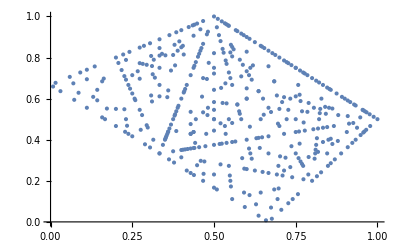

```mathematica
ListPlot[Flatten[Map[{Reverse[Last[First[#]]],Last[First[#]]}&,draw],1]]
```

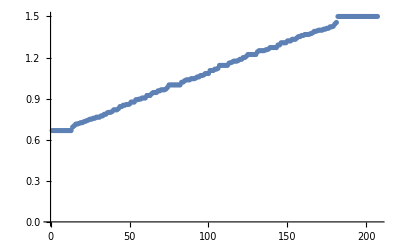

```mathematica
ListPlot[Map[Total[Last[First[#]]]&,draw],GridLines->{Automatic,{2/3,3/2}}]
```

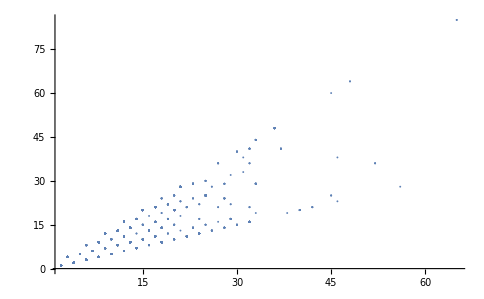

```mathematica
ListPlot[
Monitor[
Table[
With[{record=deps2[[k]]},
With[
{rule=Read[StringToStream[record[[3]]]]},
With[
{g=MyEdgeDelete[ReadGrof[record[[1]]],{rule[[2]]}]},
With[
{div=ChromaticPolynomial[g,4],vert=ChromaticPolynomial[ReadGrof[record[[2]]],4]},
{div,vert}/24
]
]
]
],
{k,1,10000}
],
k],
PlotRange->All
]
```

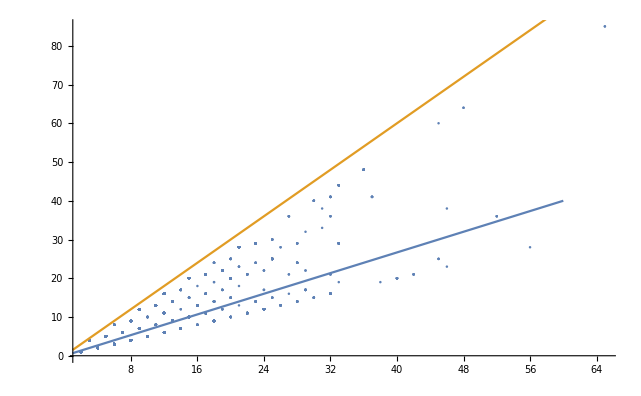

```mathematica
Show[%,Plot[{2/3x,3/2x},{x,1,60}]]
```